#### Death Rate Allometry

```mathematica
q0[Masym_]:=.0124*Masym^(-.56)
α[Masym_]:=.709*Masym^(-.27)
```

```mathematica
deathcurve[n0_,Masym_,t_]:=n0*E^((q0[Masym]/α[Masym])*(1-E^(α[Masym]*t)))
```

```mathematica
deathcurve[100,1,1]
```

98.2114

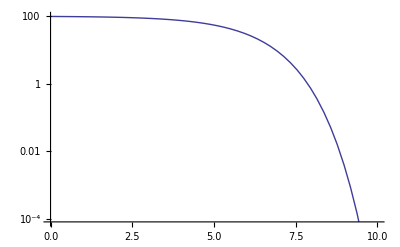

```mathematica
LogPlot[deathcurve[100,1,t],{t,0,10}]
```

```mathematica
n=n0*E^((q/a)*(1-E^(a*t)))
```

ⅇ^(((1-ⅇ^(a t)) q)/a) n0

```mathematica
specificrate=FullSimplify[D[n,t]/n]
```

-ⅇ^(a t) q

```mathematica
FullSimplify[specificrate*n/D[n,t]]
```

1

#### Damuth’s law predicionts with a variable death rate

```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final_CPK_Variations/Ratesfunc.nb"];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->(ConsumerGrowth-i*Mortality),μ->Mortality,β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
dimH/.{i->.01,M->10^5}
```

0.00199235

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"];
```

```mathematica
Hvariations={};
Fvariations={};
Do[

Hforplt=dimH/.{i->j};
Fforplt=dimF/.{i->j};


Hvariations=Append[Hvariations,LogLogPlot[Hforplt/M,{M,1,10^12},PlotStyle->Hue[j/.2]]];
Fvariations=Append[Fvariations,LogLogPlot[Fforplt/M,{M,1,10^12},PlotStyle->Hue[j/.2]]]
,
{j,-.05,.05,.0025}
]
```

```mathematica
dataplt=ListLogLogPlot[data,PlotRange->{{1,10^12},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}];
```

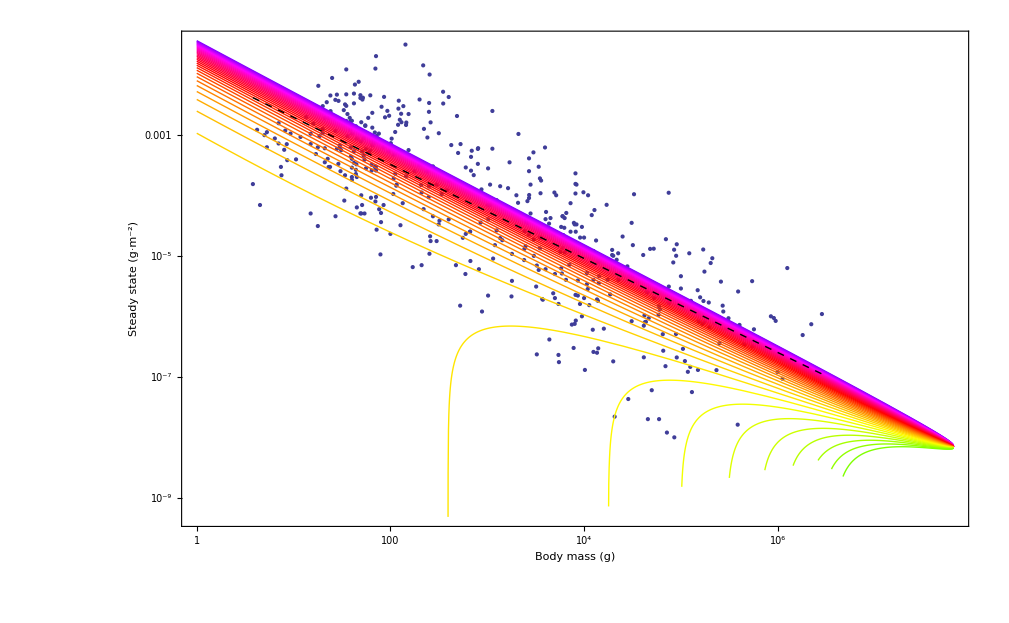

```mathematica
Show[dataplt,Fvariations,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],PlotRange->All]
```

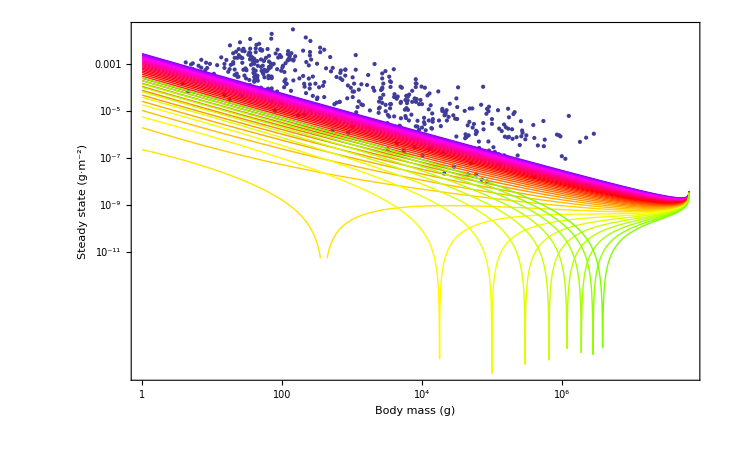

```mathematica
Show[dataplt,Hvariations,PlotRange->All]
```

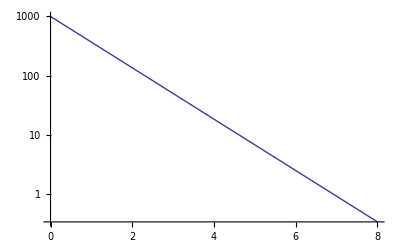

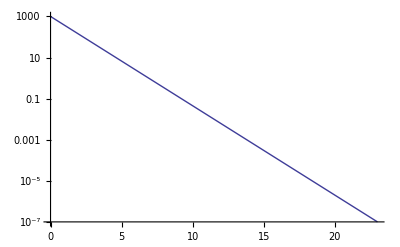

```mathematica
LogPlot[1000*E^(-x),{x,0,8}]
LogPlot[1000*E^(-x),{x,0,23}]
```

```mathematica
NSolve[1000*E^(-i*21.5)==1,i]
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{i→0.321291}}

```mathematica
D[1000*E^(-x),x]/(1000*E^(-x))*1/(365*24*3600.)
Mortality/.{M->10^1}
ConsumerGrowth/.{M->10^1}
```

-3.17098×10^-8

7.50435×10^-6

2.20234×10^-7

```mathematica
D[1000*E^(-0.321*x),x]/(1000*E^(-0.321*x))*1/(365*24*3600.)
Mortality/.{M->10^5}
ConsumerGrowth/.{M->10^5}
```

-1.01788×10^-8

5.99886×10^-7

2.09997×10^-8

```mathematica
Rstar =RSS;
Hstar =HSS;
Fstar = FSS;
StarRates={Rstar,Hstar,Fstar}/.{λ->(ConsumerGrowth-i*(2*10^(-8))),μ->(Mortality+i*(2*10^(-8))),β->FullMaintenance,δ->StarveMaintenance,α->ResourceGrowth,σ->Starvation,ρ->Recovery};
dimR = dimRSS[StarRates[[1]]];
dimH = dimSS[StarRates[[2]]];
dimF = dimSS[StarRates[[3]]];
```

```mathematica
dimH/.{i->.01,M->10^5}
```

0.00370281

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"];
```

```mathematica
Hvariations={};
Fvariations={};
HFvariations={};
Do[

Hforplt=dimH/.{i->j};
Fforplt=dimF/.{i->j};


Hvariations=Append[Hvariations,LogLogPlot[Hforplt/M,{M,1,10^12},PlotStyle->Hue[j/2]]];
Fvariations=Append[Fvariations,LogLogPlot[Fforplt/M,{M,1,10^12},PlotStyle->Hue[j/2]]];
HFvariations=Append[HFvariations,LogLogPlot[(Hforplt+Fforplt)/M,{M,1,10^12},PlotStyle->Hue[j/2]]]
,
{j,0,1,.1}
]
```

```mathematica
dataplt=ListLogLogPlot[data,PlotRange->{{1,10^12},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}];
```

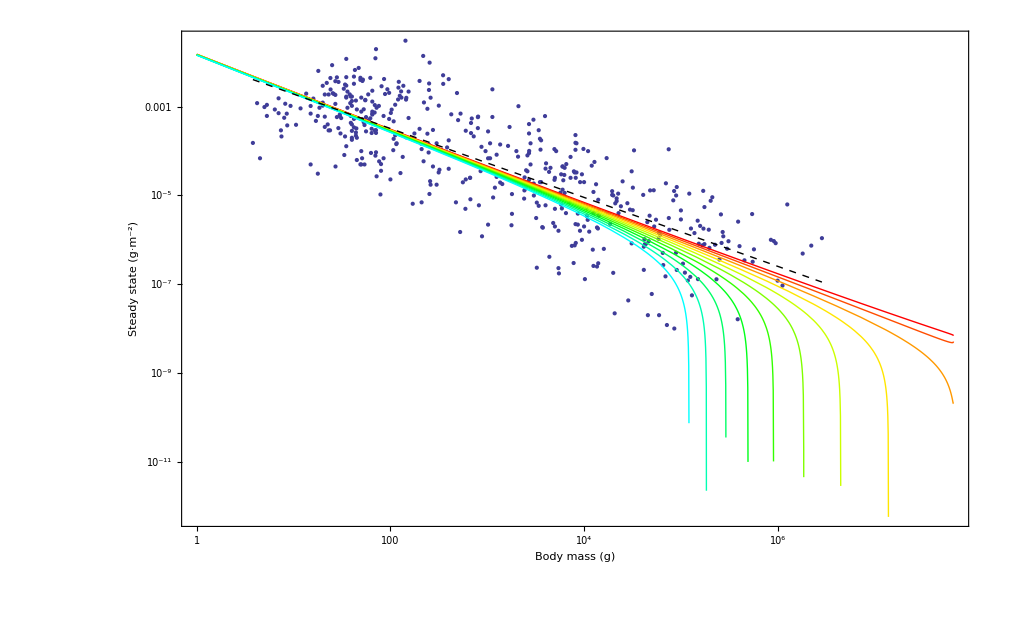

```mathematica
Show[dataplt,Fvariations,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],PlotRange->All]
```

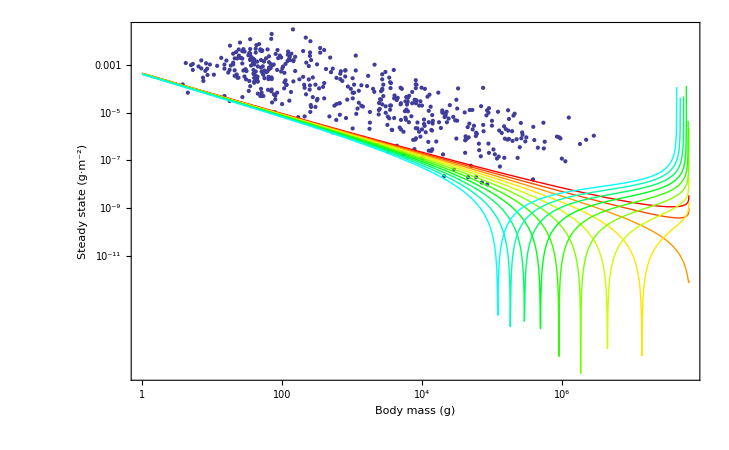

```mathematica
Show[dataplt,Hvariations,PlotRange->All]
```

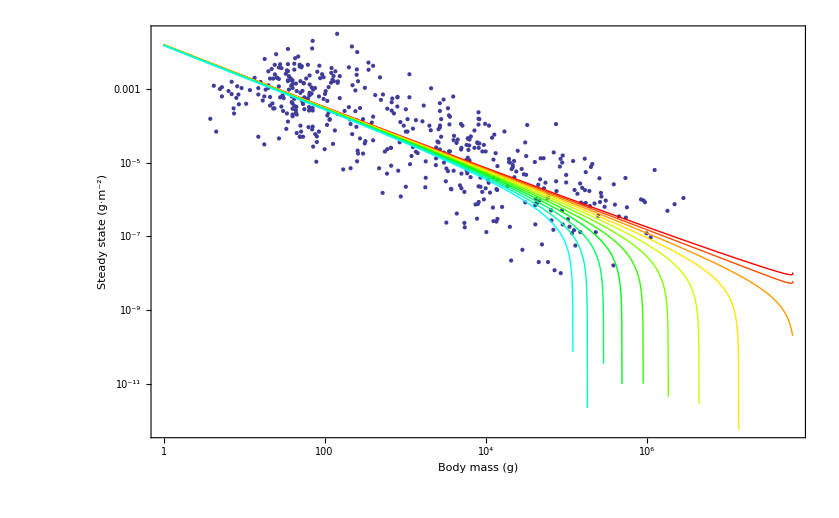

```mathematica
Show[dataplt,HFvariations,PlotRange->All]
```

Energy equivalence hypothesis

```mathematica
data = Import["/Users/chriskempes/Documents/Dropbox/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/densitydata.csv"];
```

```mathematica
Mean[data[[All,2]]]
```

0.000791639

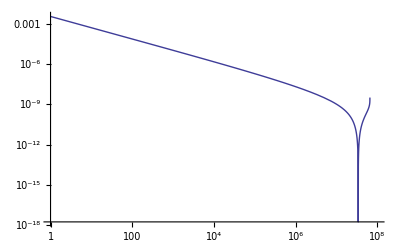

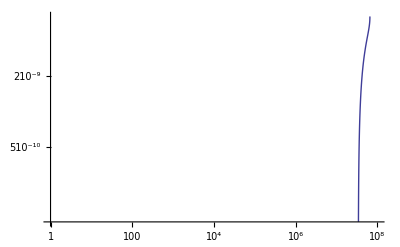

```mathematica
LogLogPlot[dimH/M,{M,1,10^8}]
LogLogPlot[dimF/M,{M,1,10^8}]
```

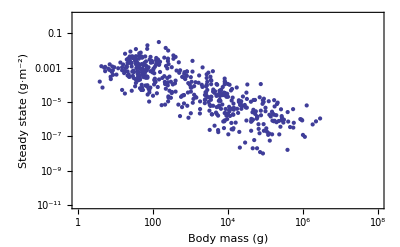

```mathematica
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}]
```

ColorData::notent: 97 is not a known entity, class, or tag for ColorData. Use ColorData[] for a list of entities.

General::stop: Further output of ColorData :: notent will be suppressed during this calculation.

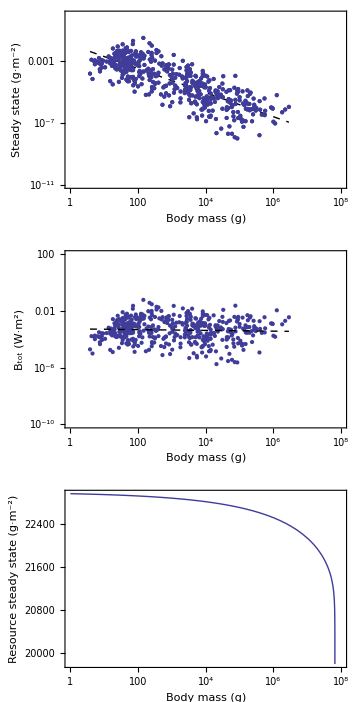

```mathematica
Cplot=GraphicsGrid[{{
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data]
}]
},{
Show[{
ListLogLogPlot[Table[{data[[i]][[1]],data[[i]][[2]]*(data[[i]][[1]])^(3/4)*B0},{i,Length[data]}],PlotRange->{{1,10^8},{10^-10,100}},Frame->True,FrameLabel->{"Body mass (g)","B_tot (W·m^2)"}],
LogLogPlot[0.0115643*M^(-0.776818)*M^(3/4)*B0,{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
LogLogPlot[{dimH/M*M^(3/4)*B0,dimF/M*M^(3/4)*B0},{M,1,10^8},Frame->True,FrameLabel->{"Body mass (g)","B_tot"},PlotStyle->{ColorData[97,2],ColorData[97,3]}]}]
},{
LogLinearPlot[dimR,{M,1,10^8},Frame->True,PlotRange->All,FrameLabel->{"Body mass (g)","Resource steady state (g·m^-2)"}]
}}]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf"}],Cplot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_FPAllometric.pdf

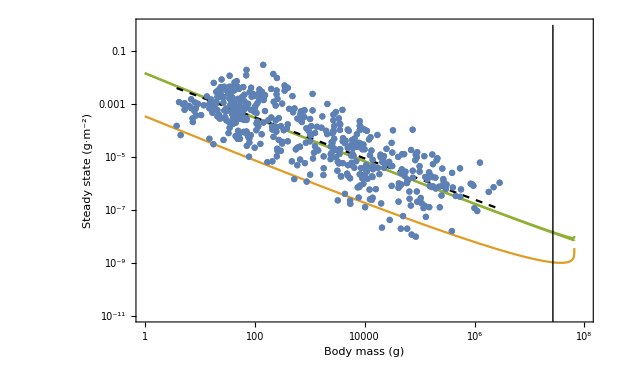

```mathematica
Show[{
ListLogLogPlot[data,PlotRange->{{1,10^8},{10^-11,1}},Frame->True,FrameLabel->{"Body mass (g)","Steady state (g·m^-2)"}],
LogLogPlot[{dimH/M,dimF/M},{M,1,10^8},PlotStyle->{ColorData[97,2],ColorData[97,3]}],
LogLogPlot[(dimH/M)+(dimF/M),{M,1,10^8},PlotStyle->ColorData[97,3]]
,LogLogPlot[0.0115643*M^(-0.776818),{M,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Directive[{Black,Dashed}]],
ListLogLogPlot[data],
Graphics[Line[{{Log@(2.66312453830273*^7),Log@(10^-15)},{Log@(2.66312453830273*^7),Log@(1)}}]]
}]
```

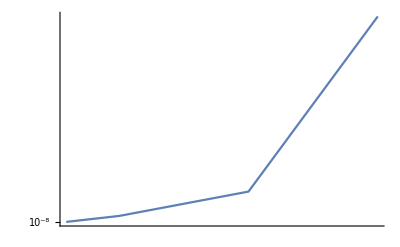

```mathematica
LogLogPlot[dimH/M+dimF/M,{M,5*10^7,10^8},PlotRange->{10^-8,All}]
```

```mathematica
Solve[f0*M^γ/M==1,M]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{M→8.30239×10^8}}

```mathematica
FindMinimum[dimR,M]
```

FindMinimum::nrnum: The function value 8380.71+288.78 ⅈ is not a real number at {M} = {2.08076×10^8}.

{8702.7,{M→1.8916×10^7}}

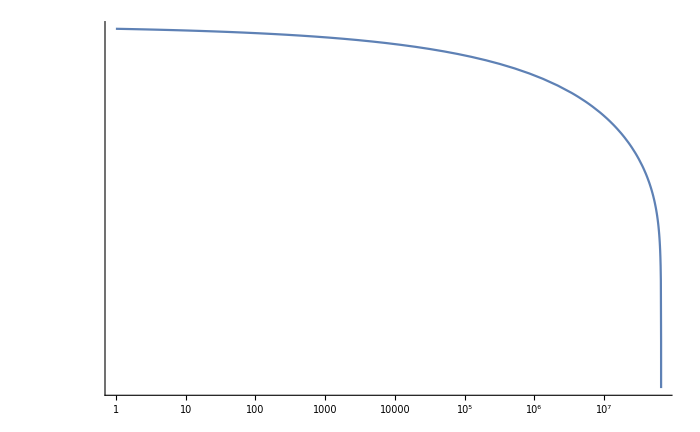

```mathematica
LogLogPlot[dimR,{M,1,10^10},PlotRange->{1000,All}]
```

```mathematica
FindMinimum[Re[StarRates[[1]]],M]
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.255557,{M→6.53794×10^7}}

```mathematica
Reduce[0.95*(1+chi)<1]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

chi<0.0526316